General parameter-shift rules for quantum gradients

Original authors of paper: David Wierichs, Josh Izaac, Cody Wang, and Cedric Yen-Yu Lin
Paper Quantum-journal (2022): https://quantum-journal.org/papers/q-2022-03-30-677/#
e-print: arXiv:2107.12390v3
Notebook: Óscar Amaro, September 2023 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

Official repo from paper from the original authors: https://github.com/dwierichs/General-Parameter-Shift-Rules

## Proof ∑_(k=1)^(n-1) tan((k π)/(2n))^2 = ((n-1)(2 n-1))/3

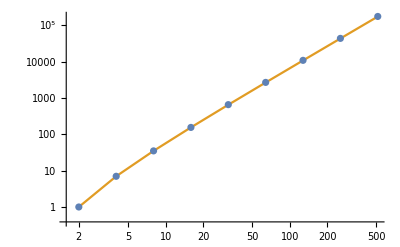

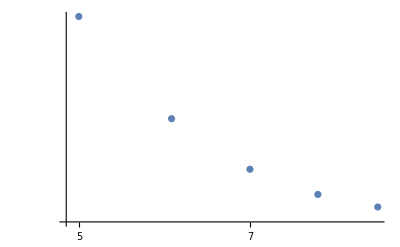

```mathematica
Clear[k,n,getSum,tab,tab2,nmax]
getSum[n_]:=NSum[Tan[(k π)/(2n)]^2,{k,1,n-1}]//Quiet
nmax=9;
tab=ParallelTable[{2^n,getSum[2^n]},{n,1,nmax,1}];
tab2=ParallelTable[{2^n,((2^n-1)(2 2^n-1))/3},{n,1,nmax,1}];

ListLogLogPlot[{tab,tab2},Joined->{False, True}]
(* there is some numerical error for larger n, but it is negligible *)
ListLogLogPlot[((tab2-tab)/tab2)[[All,2]]//Chop//Abs]
```

## Appendix A

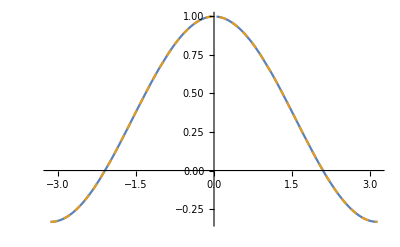

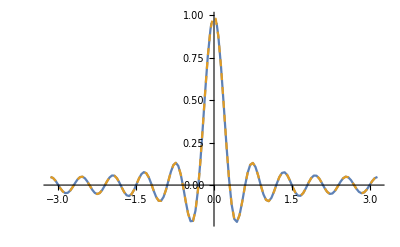

```mathematica
Clear[R,x,l]

(* R needs to be integer > 1*)
R=1;
Plot[{Sin[(2R+1)/2 x]/((2R+1)Sin[1/2 x]),1/(2R+1)+2/(2R+1)NSum[Cos[l x],{l,1,R}]},{x,-π,π},PlotPoints->3, PlotStyle->{Default,Dashed},PlotRange->All]

R=10;
Plot[{Sin[(2R+1)/2 x]/((2R+1)Sin[1/2 x]),1/(2R+1)+2/(2R+1)NSum[Cos[l x],{l,1,R}]},{x,-π,π},PlotPoints->3, PlotStyle->{Default,Dashed},PlotRange->All]
```